## Op Amps and RC Filters

## Analog Electronics, 2026-04-03

## Resistance and RC Time Constant Problems from Grisha

### 1. Both Series and Parallel Resistors in the Same Circuit!!

Hint: First collapse the two 3kΩ resistors that are in parallel into a single equivalent resistor using

R_equivalent=1/(1/R_1+1/R_2)

You should get something smaller than either R_1 or R_2. Now that it is collapsed into a single equivalent resistor, you have an ordinary voltage divider problem.

### 2. RC Time Constants — These are Tricky!! Don’t stress if you can’t do (b), (c), and (d).

Do (a) before looking at the hint/discussion below.

HINT/DISCUSSION ON (b), (c), and (d): 

You can make rough estimates by putting T=R C into the exact answer,

V(t) = V_0(1-e^(-t/T)),

and then graphing it. On the facing page is a graph that is sufficiently detailed, that you should be able to read off the times to the nearest thousandth or so of a second.

For part (d) you just take the inverse of the time to go from 1V to 3V and you have the number of times per second that can happen. Then divide by 2, to account for both charge and discharge.

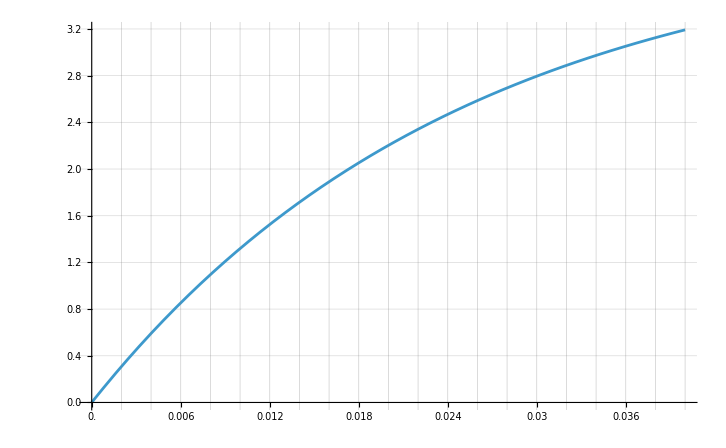

```mathematica
spacings={Range[0.000,0.040,0.002],Automatic};
f[t_]:=4(1-Exp[-t/T]);
Plot[f[t],{t, 0.0,0.04}, Ticks->spacings, GridLines->spacings]
```

## Op Amps in Non-Inverting Configuration from Victoria

### 3. Determining V_in

### 4. Determining some possible values of R_1 and R_2

-Graphics-

## Op Amps in Inverting Configuration from Nik

### 5. Determining V_out

If...
        V_in = 0.5 V
        R_1 = 2 kΩ
        R_2 = 8 kΩ

What is V_out?

### 6. Determining V_in

If...
        V_out = -9 V
        R_1 = 5 kΩ
        R_2= 15 kΩ

What is V_in?

### BONUS

Is it possible to solve for V using Ohm’s law instead of the inverting configuration formula?

## RC Low-Pass Filter from Brian

If f is the frequency of a signal, usually specified in Hz, and C is a capacitance, usually measured in microfarads, nanofarads, or picofarads, then there is a strange sense in which 1/(2 π f C) can be thought of as a resistance. A capacitor is not really a resistor, but go along with it. At least this combination has the units of Ohms, like a resistor! On the next page are some problems that build on this weird idea.

### 7. A Strange Way of Thinking about Capacitors — High Frequencies Pass Easier Through a Capacitor than Low Frequencies

(a) If a capacitor has capacitance C=100 nF (nanofarads) and a low-frequency signal with frequency f=50Hz is applied, what is the “not really a resistance” resistance of the capacitor? Call your answer R' and round to the nearest significant figure. You will use this result in 8(a).

(b) If the same capacitor has an f=5000Hz signal applied to it, what is the “not really a resistance” resistance? Call that R'' and again round to the nearest significant figure. You will use this result in 8(b).

CROSSCHECK: Your answer for (b) should be 100x smaller than your answer for (a). Notice that a capacitor’s “not really a resistance” resistance decreases as frequency increases.

### 8. Thinking of a Capacitor as a Resistor in a Voltage Divider

If the capacitor labeled C was actually a resistance with R'=1/(2π fC), then in that case you should be able to see that V_out is in a voltage divider configuration and you’d have:

V_out=V_in R'/(R+R')

The capacitor is not a resistor. Weirdly, the actual relation is:

V_out=V_in R'/(√(R^2+R'^2))

(a) If R=3000Ω, and the applied signal V_in has size 10V and frequency 50Hz, and using your answer for R' from 7(a) what is V_out=V_in R'/(√(R^2+R'^2))?

(b) Keeping R=3000Ω, and V_in having size 10V, but this time f=5000Hz, and using your answer for R'' from 7(b), what is V_out=V_in R''/(√(R^2+R''^2))?